# Highly-cited articles

## 登録論文数累積

edgestat-refcount-cumulative.nb より。

```mathematica
artcountAcm={331362,866254,1415896,2141764,3156527,4323230,5675522,7217673,9135438,11279956,13673661,16645203,20421796,25376280,31440632}
```

{331362,866254,1415896,2141764,3156527,4323230,5675522,7217673,9135438,11279956,13673661,16645203,20421796,25376280,31440632}

## 累積世代ごとの主要論文

```mathematica
mainartfiles=Table["/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-"<>ToString[n]<>"_topCitingCitedArt1Perc.save",{n,1950,2020,5}]
```

{/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1950_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1955_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1960_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1965_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1970_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1975_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1980_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1985_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1990_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1995_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2000_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2005_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2010_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2015_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2020_topCitingCitedArt1Perc.save}

```mathematica
Map[Get,mainartfiles];
```

### 主要論文

主要論文PMIDと被引用数

```mathematica
(top1PcCitedArtList=Table[Reverse[SortBy[Flatten[Map[#[[2]]&,topCitingCitedArt1Perc[n,"citing rule"],{2}]]//Tally,#[[2]]&]],{n,1950,2020,5}])//Length
```

15

主要論文数

```mathematica
top1PcCitedArtCount=Map[Length,top1PcCitedArtList]
```

{10,30,46,50,38,33,32,26,19,22,33,66,192,315,336}

全論文数における主要論文数割合（%）

```mathematica
top1pcArtRatio=top1PcCitedArtCount/artcountAcm*100//N
```

{0.00301785,0.00346319,0.00324883,0.00233452,0.00120385,0.000763318,0.000563825,0.000360227,0.000207981,0.000195036,0.00024134,0.000396511,0.000940172,0.00124132,0.00106868}

### 新規出現論文

```mathematica
FoldList[Composition[Union,Flatten,List],{},Map[#[[1]]&,top1PcCitedArtList,{2}]];
```

新規出現主要論文ID

```mathematica
newcomerCitedArt=Map[Complement[#[[2]],#[[1]]]&,Partition[FoldList[Composition[Union,Flatten,List],{},Map[#[[1]]&,top1PcCitedArtList,{2}]],2,1]]
```

{{16694480,16694558,16695228,16747456,16747508,16747784,17247100,17247150,17751251,18016252},{14772207,14822727,14907713,15395398,15398090,15398551,16561366,16695286,16695568,16745305,16746620,16747230,16747652,16747674,16747907,16747948,16748220,16748273,16748381,16991878,17760012,18128147},{12989928,12991232,12991237,12996882,13069686,13124776,13130792,13186838,13319380,14381428,14803635,14862161,14873923,14898516,14907661,14915960,14927794,15392854,15395569,15404816,15410483,15421999,15436457,16991506,16994401},{13249955,13262900,13276348,13286333,13293190,13428781,13475399,13563554,13610936,13718526,13764136,13975866,13986422,14381429,14454024,14775715,14794694,14848424,14927572,14938350},{13610928,13641241,13675766,13767412,13772379,13944428,14240539,14287192,14474176},{13267987,13278318,13672998,13910995,16654194,4956917,5806584},{1195397,13671378,14097352,4850204,4887011,5432063,5962951,773363},{236308,265521,271968,388356,388439,4326772,6159641,6246368,881736,942051},{518835,6312838},{2440339,2448875,2985470,6270629,6546423},{2231712,4705382,6336730,6828386,6960240,7108955},{1172191,149110,2025413,2199796,2659436,3162770,322279,3323813,344137,3447015,3838314,3843705,3881765,4179068,4291934,4504350,6091052,6166661,6235151,6266278,6295879,6310323,6326095,6329026,6345791,7984417,9254694},{10069079,10547847,10592235,10647931,10655437,10802651,10829079,1105573,11130711,11181995,11237011,11309499,11328886,11368702,11373684,11498575,11524383,1175627,11846609,1202204,12466850,12748199,12824337,12912839,12925520,13650640,13688369,1400587,14399272,14450081,14530136,14744438,15034147,15260895,15297300,15299374,15299926,15461798,1555235,15572765,15761078,1593914,16255080,16595758,17237035,17488738,17554300,18156677,18287387,1852778,19171970,2439888,2449095,2744487,27754618,28561359,2868172,291033,2999980,3047011,320200,3327686,3344216,3358796,3537305,3558716,3670292,3692487,3714490,3806354,3899825,4202581,4337382,4366476,4598299,4896022,5146491,5700707,5963888,603028,6198242,6232463,6253831,6260957,6269464,6286831,6295880,6310324,6329717,6606682,6610841,6667333,6791577,6880820,7138600,7219534,7463489,7494007,8223268,8242752,8254673,8366922,843571,8520220,8744570,8744573,8902363,9177342,922889,9278503,9367129,9396791,9486653,9504803,9521319,9521921,9634230,9717241,9742976,9757107,9843981,9887164,9918953},{10075613,10102814,10109801,10592173,10638745,10797032,10827456,10835412,10963602,11152613,11209064,11234459,11283309,11553815,11556941,11689955,11752295,11771995,11823860,11832527,11904577,11932250,11994752,12045153,12068308,12111919,12117397,12130773,12184808,12297042,1244564,12485966,12490959,12538238,12629218,12734009,12883005,12958120,13298683,13655060,13726518,14597658,14656957,15111519,15118073,15118125,15173120,15175435,15223320,15264254,15372042,15501092,15652477,15758009,15939837,15944708,16056220,16081474,16199517,16222654,16497588,16646809,16862161,16904174,16928733,17320507,17483113,17512414,1759558,17618441,17634462,17681537,17701901,17846036,17996036,18029452,18035408,18261238,18349386,18485877,18516045,18546601,18772890,18839484,19015660,19033363,19097774,19131956,19167326,19261174,19289445,19325852,1932883,19451168,19461840,19474385,19505943,19565683,19801464,19812666,20057044,20124692,20124702,20354512,20383002,20383131,20436464,20525992,20610543,20644199,20979621,20981092,21296855,21351269,21376230,21460441,21546353,2188735,22237781,22930834,22955616,23335087,24132122,24399786,24889800,2513255,2748771,3397865,3616518,36810,3798106,3802833,3928249,4561027,6668417,7063747,7786990,7814313,7984236,8252621,8421494,8524021,8589427,8628042,8721797,8779443,8812068,9023104,9176952,9305837,9310563,9521922,9623998,9759494,9804556,9881538,9916792,9944570},{10062328,10789670,11253156,12377157,12391568,12900694,15102499,15273542,15817019,15969739,16055882,16204405,16820507,16923388,16923606,17183312,17486113,17586664,17695343,17872937,1798888,18650514,18650914,18798982,18929686,19029910,19114008,19246619,19346325,19414839,19460998,19487818,19499576,19621072,19622511,19622551,19805654,19910308,19945376,20003500,20080505,20110278,20513432,20525638,20601685,20709691,21221095,21478889,21572440,21700674,21816040,21959131,21988835,22008217,22357727,22383036,22388286,22437870,22506599,22543367,22588877,22658127,22743772,22745249,22820204,23000897,23104886,23128226,23193283,23245604,23287718,23329690,23550210,23618408,24141714,24451623,24695404,25220842,25260700,25516281,25554246,25559415,25567568,25605792,25651787,25741868,26432245,26742998,26808342,26903338,27004904,27535533,28055103,29313949,30207593,30620402,31978945,31986264,32007143,3203132,32031570,32109013,32171076,9931268}}

新規出現主要論文数

```mathematica
newcomerCitedArtCount=Map[Length,newcomerCitedArt]
```

{10,22,25,20,9,7,8,10,2,5,6,27,123,158,104}

主要論文数における新規出現論文数割合（%）

```mathematica
newcomerratio=newcomerCitedArtCount/top1PcCitedArtCount*100//N
```

{100.,73.3333,54.3478,40.,23.6842,21.2121,25.,38.4615,10.5263,22.7273,18.1818,40.9091,64.0625,50.1587,30.9524}

### plot

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/exec_command/generations.wl"]
```

{1950,1955,1960,1965,1970,1975,1980,1985,1990,1995,2000,2005,2010,2015,2020}

```mathematica
ListPlot[{top1PcCitedArtCount,newcomerCitedArtCount},Joined->True,PlotRange->Full,Frame->True,FrameTicks->{Automatic,{genticks,None}},PlotLabels->{"主要論文数","新規出現主要論文数"}]
```

-Graphics-

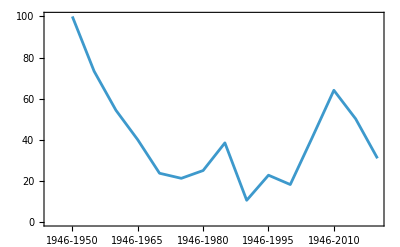
-Graphics-新規出現主要論文の全主要論文に占める割合（%）

```mathematica
Labeled[ListPlot[newcomerratio,Joined->True,Frame->True,FrameTicks->{Automatic,{genticks,None}}],"新規出現主要論文の全主要論文に占める割合（%）"]
```

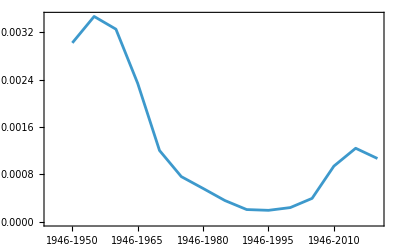
-Graphics-主要論文の全論文に占める割合（%）

```mathematica
Labeled[ListPlot[top1pcArtRatio,Joined->True,Frame->True,FrameTicks->{Automatic,{genticks,None}}],"主要論文の全論文に占める割合（%）"]
```

## 主要論文タイトル

PMIDから論文タイトルを引く

プログラム

```mathematica
st=Import["/Volumes/elecom/BANK/pubmed/202312/xml/element/title/pubmed24n0080.xml.blk","String"];
```

```mathematica
st1=Drop[StringSplit[st,"<PubmedArticle>"],1];
```

```mathematica
st2=Map[StringSplit[#,"\n"]&,StringSplit[st1,"\n--\n"],{2}];
```

```mathematica
st3=Map[StringReplace[#,RegularExpression["\\[\\[\\[.*\\]\\]\\]"]->""]&,st2,{3}];
```

```mathematica
titlecase[l_]:=Cases[l,{x_,y_}/;StringMatchQ[x,"<PMID *"]||StringMatchQ[x,"<ArticleTitle>"]]
```

```mathematica
(st3case=Map[titlecase,st3])//Length
```

30000

```mathematica
st3case2=Map[#[[1;;2]]&,Select[st3case,Length[#]>=2&]]
```

```mathematica
st3rule=MapApply[Rule,Map[#[[2]]&,st3case2,{2}]]
```

```mathematica
blkToTitleRule[file_String]:=Module[{st,st1,st2,st3,st3case,st3case2,st3rule},
st=Import[file,"String"];
st1=Drop[StringSplit[st,"<PubmedArticle>"],1];
st2=Map[StringSplit[#,"\n"]&,StringSplit[st1,"\n--\n"],{2}];
st3=Map[StringReplace[#,RegularExpression["\\[\\[\\[.*\\]\\]\\]"]->""]&,st2,{3}];

st3case=Map[titlecase,st3];
st3case2=Map[#[[1;;2]]&,Select[st3case,Length[#]>=2&]];
st3rule=MapApply[Rule,Map[#[[2]]&,st3case2,{2}]]
]
```

プログラム適応

```mathematica
(blks=FileNames["/Volumes/elecom/BANK/pubmed/202312/xml/element/title/*blk"])//Length
```

1219

```mathematica
(*AbsoluteTiming[(pmidToTitle=Association[Flatten[ParallelMap[blkToTitleRule,blks]]]);]*)
```

$Aborted

```mathematica
(*Save["/Volumes/elecom/BANK/pubmed/202312/xml/element/title/"<>"pmidToTitle.save",pmidToTitle]*)
```

高被引用論文タイトル

ルールを読み込む

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/title/"<>"pmidToTitle.save"];
```

```mathematica
top1pctitle=Map[{pmidToTitle[#[[1]]],#[[2]]}&,top1PcCitedArtList,{2}];
```

```mathematica
(*Save["/Volumes/elecom/BANK/pubmed/202312/xml/element/title/"<>"top1pctitle.save",top1pctitle]*)
```

### 代表リスト

考え中